## ECEN 4005 - Homework 5

#### Problem 1(a)

```mathematica
V1 = Cos[ω01*t]*ℏ*Ω01;
FullSimplify[InverseFourierTransform[V1,t,ω,FourierParameters->{-1,1}]]
```

π Ω01 ℏ DiracDelta[ω-ω01]+π Ω01 ℏ DiracDelta[ω+ω01]

```mathematica
V2 = Cos[ω01*t]*ℏ*Ω01*ⅇ^(-t^2/(2*tgate^2));
FullSimplify[InverseFourierTransform[V2,t,ω,FourierParameters->{-1,1}]]
```

ⅇ^(-1/2 tgate^2 (ω+ω01)^2) (1+ⅇ^(2 tgate^2 ω ω01)) √(π/2) √(tgate^2) Ω01 ℏ

```mathematica
FullSimplify[Expand[ⅇ^(-1/2 tgate^2 (ω+ω01)^2) (1+ⅇ^(2 tgate^2 ω ω01))]]
```

ⅇ^(-1/2 tgate^2 (ω+ω01)^2) (1+ⅇ^(2 tgate^2 ω ω01))

#### Problem 1(b)

```mathematica
hmat = (ℏ/2*Ω01)*{{0,1,0},{1,0,λ},{0,λ,0}}; MatrixForm[hmat]
```

(0 | (Ω01 ℏ)/2 | 0
(Ω01 ℏ)/2 | 0 | (λ Ω01 ℏ)/2
0 | (λ Ω01 ℏ)/2 | 0)

```mathematica
Eigenvalues[hmat]
```

{0,-1/2 √(1+λ^2) Ω01 ℏ,1/2 √(1+λ^2) Ω01 ℏ}

```mathematica
Eigenvectors[hmat]
```

{{-λ,0,1},{1/λ,-(√(1+λ^2))/λ,1},{1/λ,(√(1+λ^2))/λ,1}}

#### Problem 1 (c)

```mathematica
FullSimplify[(√(1+λ^2))/(λ*(2/λ+2*λ))*(ⅇ^(-I*(1/2 √(1+λ^2) Ω01 ℏ)*t/ℏ)-ⅇ^(-I*(-1/2 √(1+λ^2) Ω01 ℏ)*t/ℏ))]
```

-(ⅈ Sin[1/2 t √(1+λ^2) Ω01])/(√(1+λ^2))

```mathematica
p[t_] =(Sin[1/2 t √(1+λ^2) Ω01]^2)/(1+λ^2)
```

(Sin[1/2 t √(1+λ^2) Ω01]^2)/(1+λ^2)

```mathematica
FullSimplify[D[p[t],t]==0]
```

(Ω01 Sin[t √(1+λ^2) Ω01])/(√(1+λ^2))==0

```mathematica
Solve[t √(1+λ^2) Ω01 == π/2,t]
```

{{t→π/(2 √(1+λ^2) Ω01)}}

```mathematica
p[π/(2*Ω01*√(1+λ^2))]
```

1/(2 (1+λ^2))

#### Problem 1 (d)

```mathematica
p1new [t_] = ⅇ^(-t/T1)/(2*(1+(ⅇ^(-((Ecoverℏ*t)/(√2))^2))));
```

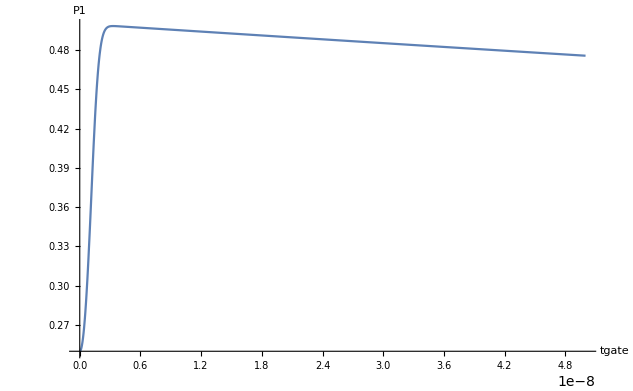

```mathematica
Ecoverℏ = 2*π*0.2*10^9;
T1 = 10^-6;
Plot[p1new[t],{t,0,50*10^-9}, PlotRange->Full, AxesLabel->{tgate,P1}]
```